```mathematica
(*Defining parameters*)
A0=100;
B0:=0.04;
h0:=2.3;
basal0:=0.1;
A1:=300;(*Modified from 184*)
B1:=0.07;(*Modified from 0.007*)
h1:=0.45;(*Modified from 0.89*)
basal1:=1.98;
A2:=57.6;
B2:=160;
h2:=3.7;
basal2:=0.52;
Aa:=0.9;
Ba:=0.072;
ha:=1.9;
basala:=0.105;
b0:=10;
b1:=43;
b2:=6;
etaN:=0;
etaG:=0.652;

Np:=1;
kr:=1/5;(*Check if minutes or seconds?*)
k:=b0*kr;
g:=1/30;(*Check if minutes or seconds*)
(*Define transfer functions*)
f0[IPTG_]:=A0/(1+(IPTG/B0)^h0)+basal0;
f1[y0A_]:=A1/(1+(y0A/B1)^h1)+basal1;
f2[y1A_]:=A2/(1+(y1A/B2)^h2)+basal2;
fa[ATC_]:=Aa/(1+(ATC/Ba)^ha)+basala;
(*Define steady state values, log gains and noises*)
y0s:=k/g;
y0As[IPTG_]:=f0[IPTG]*y0s;
y1s[IPTG_]:=(Np*f1[y0As[IPTG]])/g;
y1As[IPTG_,ATC_]:=fa[ATC]*y1s[IPTG];
y2s[IPTG_,ATC_]:=(Np*f2[y1As[IPTG,ATC]])/g;
eta2int0:=(b0+1)/y0s;
eta2int1[IPTG_]:=(b1+1)/y1s[IPTG];
eta2int2[IPTG_,ATC_]:=(b2+1)/y2s[IPTG,ATC];
eta2int3:=0;
H10[IPTG_]:=h1/(A1*f1[y0As[IPTG]])*(f1[y0As[IPTG]]-basal1)*(basal1+A1-f1[y0As[IPTG]]);
H21[IPTG_,ATC_]:=h2/(A2*f2[y1As[IPTG,ATC]])*(f2[y1As[IPTG,ATC]]-basal2)*(basal2+A2-f2[y1As[IPTG,ATC]]);
eta20:=eta2int0+etaG^2;
eta21[IPTG_]:=eta2int1[IPTG]+1/2*(H10[IPTG])^2*eta20+1/2 etaN^2+etaG^2*(1-H10[IPTG]);
eta2intTrans2[IPTG_,ATC_]:=1/2*(H21[IPTG,ATC])^2*eta2int1[IPTG]+3/8*(H21[IPTG,ATC])^2*(H10[IPTG])^2*eta2int0;
eta2G2[IPTG_,ATC_]:=etaG^2*(1+1/2*(H21[IPTG,ATC])^2+3/8*(H21[IPTG,ATC])^2*(H10[IPTG])^2-H21[IPTG,ATC]-3/4*(H21[IPTG,ATC])^2*H10[IPTG]+1/2*H21[IPTG,ATC]*H10[IPTG]);
eta22[IPTG_,ATC_]:=eta2int2[IPTG,ATC]+eta2intTrans2[IPTG,ATC]+etaN^2*(1/2+1/8*(H21[IPTG,ATC])^2-3/4*H21[IPTG,ATC])+eta2G2[IPTG,ATC];
eta23:=etaG^2+eta2int3+1/2*etaN^2;
(*Define correlations*)
C03:=etaG^2;
C12[IPTG_,ATC_]:=-1/2*H21[IPTG,ATC]*eta2int1[IPTG]-3/8*H21[IPTG,ATC]*(H10[IPTG])^2*eta2int0+etaG^2*(1-1/2*H21[IPTG,ATC]-1/2*H10[IPTG]-3/8 H21[IPTG,ATC]*(H10[IPTG])^2+3/4*H21[IPTG,ATC]*H10[IPTG])+etaN^2*(1/2-3/8*H21[IPTG,ATC]);
C13[IPTG_]:=etaG^2*(1-1/2*H10[IPTG])+1/2*etaN^2;
C23[IPTG_,ATC_]:=etaG^2*(1-1/2*H21[IPTG,ATC]+1/4*H21[IPTG,ATC]*H10[IPTG])+etaN^2*(1/2-3/8*H21[IPTG,ATC]);
```

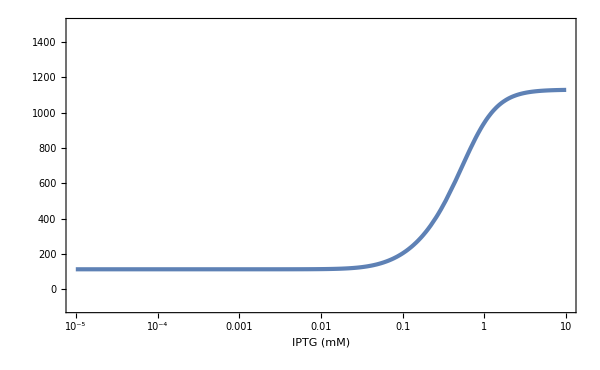

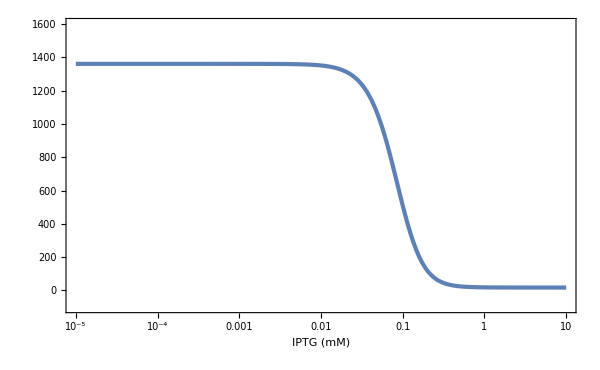

```mathematica
(*Plot Expression of gene 1 and gene 2*)
optGen = {Frame->True,PlotStyle->AbsoluteThickness[3],FrameStyle->Directive[Black,Thick],LabelStyle->Directive[30,FontFamily->"Palatino Linotype",Black],FrameLabel->{Text[Style["IPTG (mM)"]],None}};
opty1={PlotRange->{{10^-5,10},{-100,1500}}};
imSize1 = {ImageSize->600};
Gy1=Show[LogLinearPlot[y1s[IPTG],{IPTG,10^-5,10},Evaluate[optGen],Evaluate[opty1]],Evaluate[imSize1]]
Export["/home/gutiloluis/61Monograph/images/lan-y1.png",Gy1];

opty2={PlotRange->{{10^-5,10},{-100,1600}}};
Gy2=Show[LogLinearPlot[y2s[IPTG,0],{IPTG,10^-5,10},Evaluate[optGen],Evaluate[opty2]],Evaluate[imSize1]]
Export["/home/gutiloluis/61Monograph/images/lan-y2.png",Gy2];
```

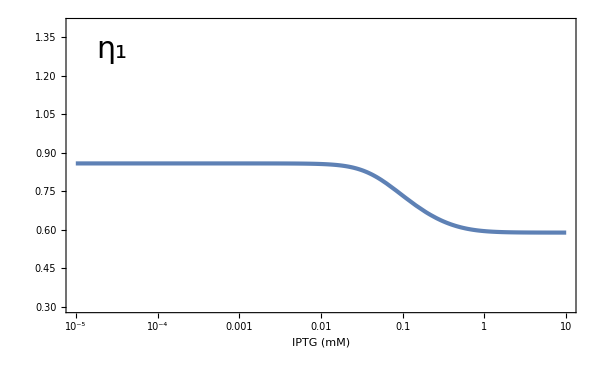

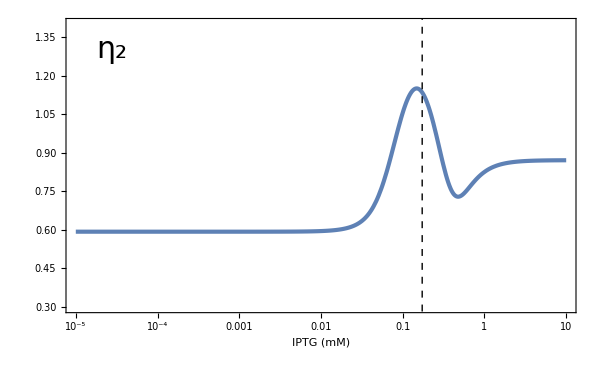

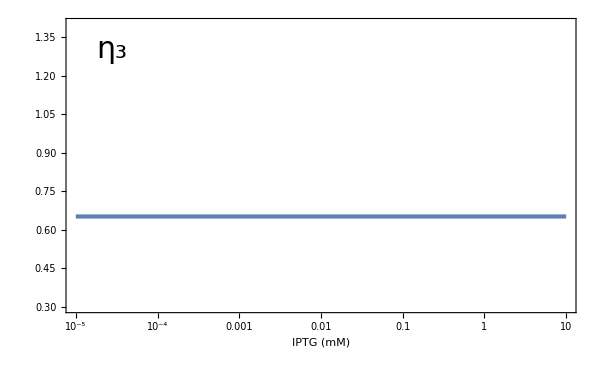

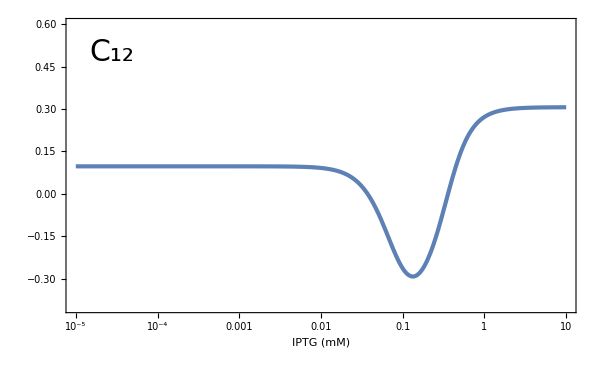

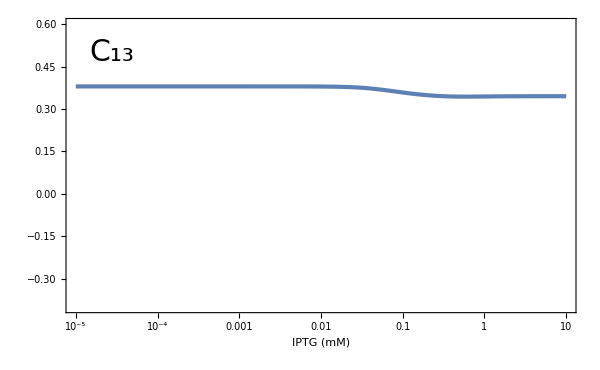

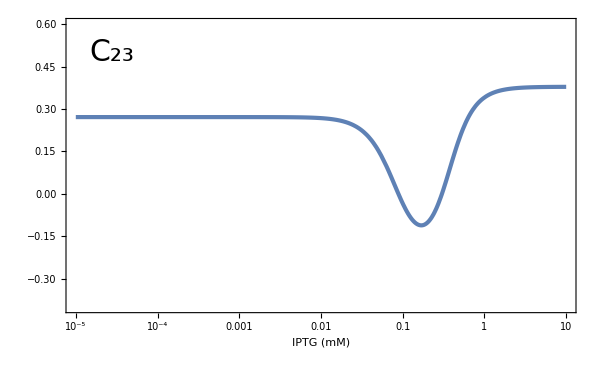

```mathematica
(*Plot noises and correlations*)
optNoise = {PlotRange->{{10^-5,10},{0.3,1.4}}};
titleSetIn = {30,Black,FontFamily->"Palatino Linotype"};
titleCoordNoise = {-10.5,1.3};
addLine = {Epilog->{Directive[Black,Dashed,Thick],Line[{{Log[0.173],5},{Log[0.173],-5}}]}};

Geta1 = Show[LogLinearPlot[Sqrt[eta21[IPTG]],{IPTG,10^-5,10},Evaluate[optGen],Evaluate[optNoise]],Graphics[Text[Style[ToExpression["\\eta_1",TeXForm,HoldForm],Evaluate[titleSetIn]],Evaluate[titleCoordNoise]]],Evaluate[imSize1]]
Export["/home/gutiloluis/61Monograph/images/lan-eta1.png",Geta1];

Geta2= Show[LogLinearPlot[Sqrt[eta22[IPTG,0]],{IPTG,10^-5,10},Evaluate[optGen],Evaluate[optNoise]],Graphics[Text[Style[ToExpression["\\eta_2",TeXForm,HoldForm],Evaluate[titleSetIn]],Evaluate[titleCoordNoise]]],
Evaluate[imSize1],Evaluate[addLine]]
Export["/home/gutiloluis/61Monograph/images/lan-eta2.png",Geta2];

Geta3=Show[LogLinearPlot[Sqrt[eta23],{IPTG,10^-5,10},Evaluate[optGen],Evaluate[optNoise]],Graphics[Text[Style[ToExpression["\\eta_3",TeXForm,HoldForm],Evaluate[titleSetIn]],Evaluate[titleCoordNoise]]],Evaluate[imSize1]]
Export["/home/gutiloluis/61Monograph/images/lan-eta3.png",Geta3];

optCorr= {PlotRange->{{10^-5,10},{-0.4,0.6}}};
titleCoordCorr={-10.5,0.5};

Gc12=Show[LogLinearPlot[C12[IPTG,0],{IPTG,10^-5,10},Evaluate[optGen],Evaluate[optCorr]],Graphics[Text[Style[ToExpression["C_{12}",TeXForm,HoldForm],Evaluate[titleSetIn]],Evaluate[titleCoordCorr]]],Evaluate[imSize1]]
Export["/home/gutiloluis/61Monograph/images/lan-c12.png",Gc12];

Gc13=Show[LogLinearPlot[C13[IPTG],{IPTG,10^-5,10},Evaluate[optGen],Evaluate[optCorr]],Graphics[Text[Style[ToExpression["C_{13}",TeXForm,HoldForm],Evaluate[titleSetIn]],Evaluate[titleCoordCorr]]],Evaluate[imSize1]]
Export["/home/gutiloluis/61Monograph/images/lan-c13.png",Gc13];

Gc23=Show[LogLinearPlot[C23[IPTG,0],{IPTG,10^-5,10},Evaluate[optGen],Evaluate[optCorr]],Graphics[Text[Style[ToExpression["C_{23}",TeXForm,HoldForm],Evaluate[titleSetIn]],Evaluate[titleCoordCorr]]],Evaluate[imSize1]]
Export["/home/gutiloluis/61Monograph/images/lan-c23.png",Gc23];
```

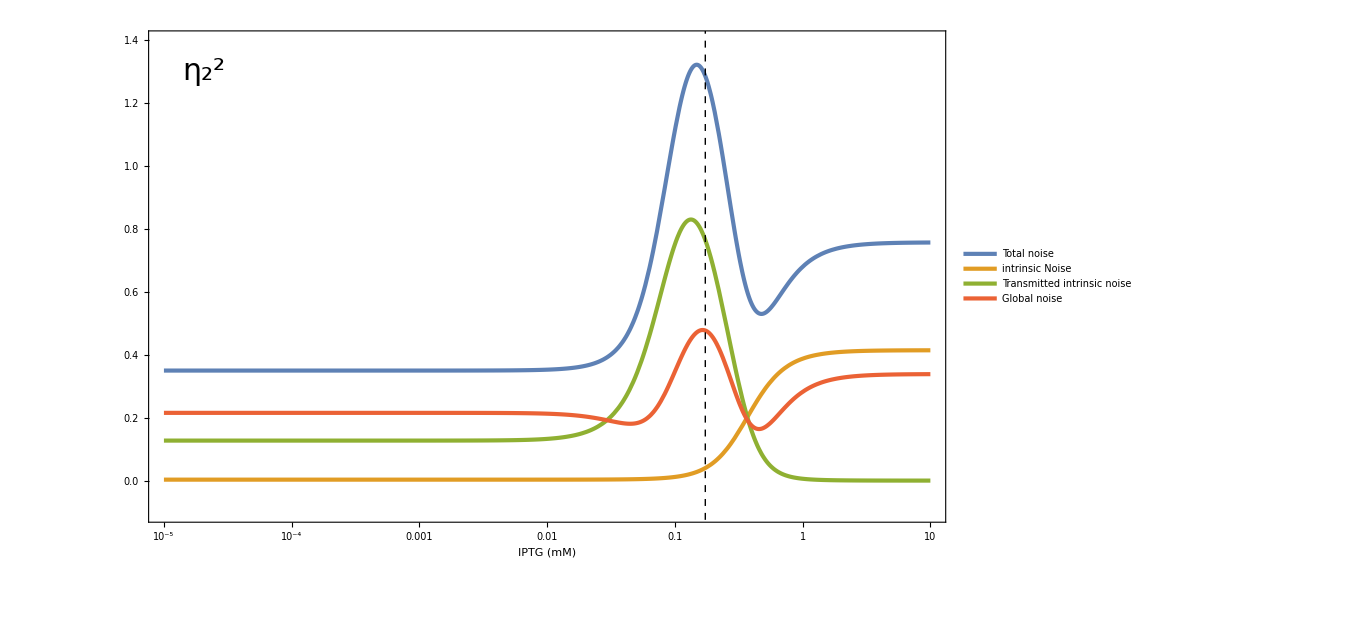

```mathematica
(*Plot of each of the noise sources for gene 2*)
optNoises = {PlotRange->{{10^-5,10},{-0.1,1.4}}};legendNoises={PlotLegends->Placed[LineLegend[{"Total noise","intrinsic Noise","Transmitted\nintrinsic noise","Global noise"},LegendMarkerSize->{30},LabelStyle->{FontFamily->"Palatino Linotype",20},LegendLayout->{"Row",4},Spacings->0.2],{0.88,0.82}]};
imSize2 = {ImageSize->1000};
titleCoordNoises = {-10.8,1.3};

Geta2det=Show[LogLinearPlot[{eta22[IPTG,0],eta2int2[IPTG,0],eta2intTrans2[IPTG,0],eta2G2[IPTG,0]},{IPTG,10^-5,10},Evaluate[optGen],Evaluate[optNoises],Evaluate[legendNoises]],Graphics[Text[Style[ToExpression["\\eta_2^2",TeXForm,HoldForm],Evaluate[titleSetIn]],Evaluate[titleCoordNoises]]],Evaluate[imSize2],Evaluate[addLine]]
Export["/home/gutiloluis/61Monograph/images/lan-eta2det.png",Geta2det];
```

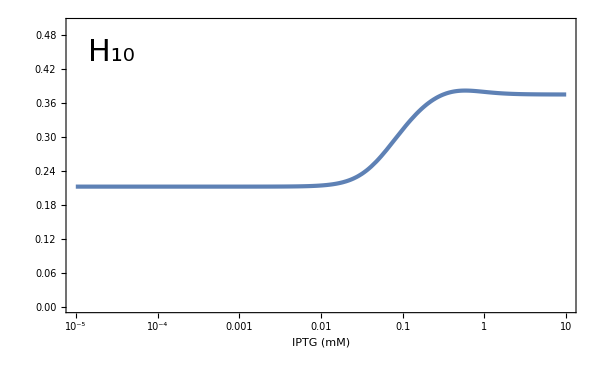

```mathematica
optH10={PlotRange->{{10^-5,10},{0,0.5}}};
titleCoordH10={-10.5,0.45};
GH10=Show[LogLinearPlot[H10[IPTG],{IPTG,10^-5,10},Evaluate[optGen],Evaluate[optH10]],Graphics[Text[Style[ToExpression["H_{10}",TeXForm,HoldForm],Evaluate[titleSetIn]],Evaluate[titleCoordH10]]],Evaluate[imSize1]]
Export["/home/gutiloluis/61Monograph/images/lan-H10.png",GH10];
```

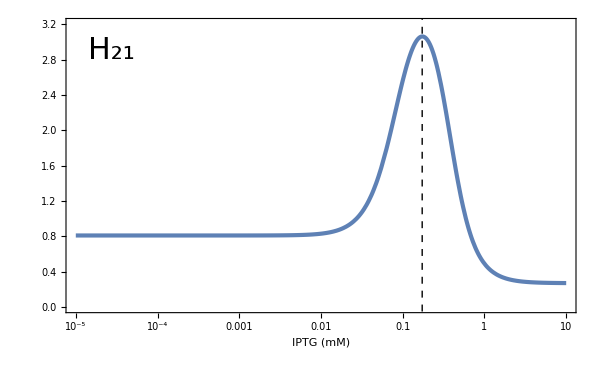

```mathematica
(*Plot H21*)
optH21={PlotRange->{{10^-5,10},{0,3.2}}};
titleCoordH21={-10.5,2.9};
GH21=Show[LogLinearPlot[H21[IPTG,0],{IPTG,10^-5,10},Evaluate[optGen],Evaluate[optH21]],Graphics[Text[Style[ToExpression["H_{21}",TeXForm,HoldForm],Evaluate[titleSetIn]],Evaluate[titleCoordH21]]],Evaluate[imSize1],Evaluate[addLine]]
Export["/home/gutiloluis/61Monograph/images/lan-H21.png",GH21];
```

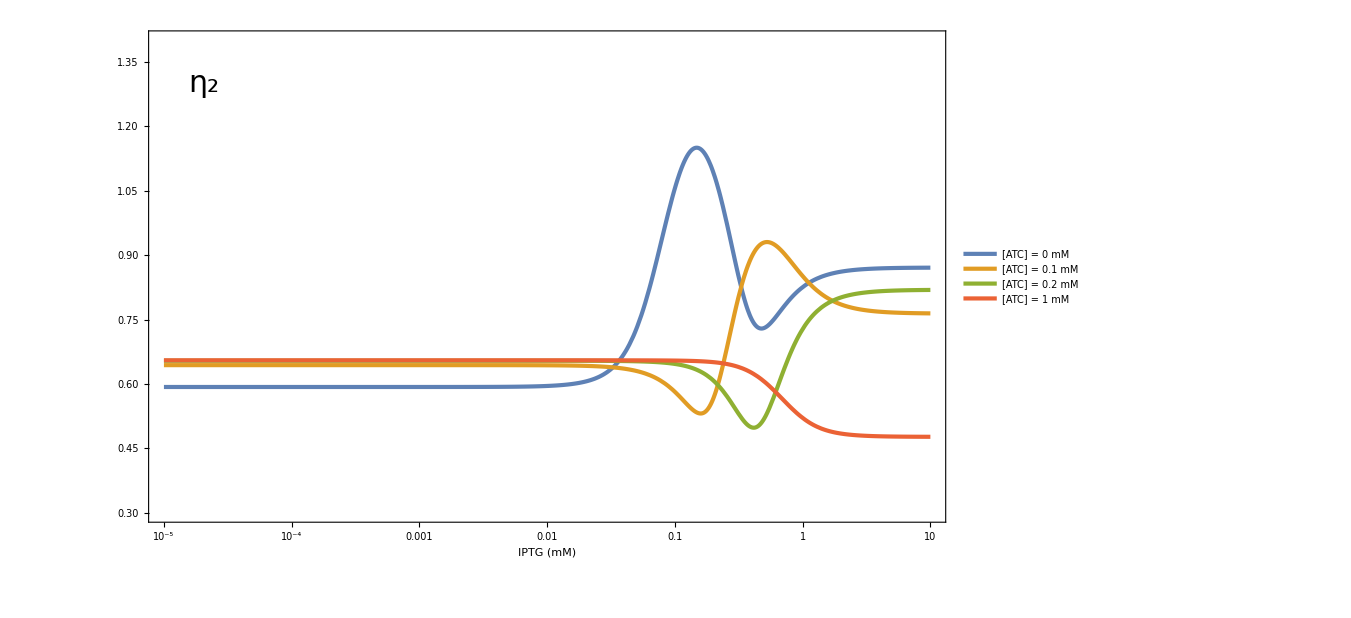

```mathematica
(*Include ATC induction*)

legendNoiseATC={PlotLegends->Placed[LineLegend[{"[ATC] = 0  mM","[ATC] = 0.1 mM","[ATC] = 0.2 mM","[ATC] = 1  mM"},LegendMarkerSize->{20},LabelStyle->{FontFamily->"Palatino Linotype",20},LegendLayout->{"Row",4},Spacings->0.2],{0.87,0.88}]};
titleCoordNoiseATC = {-10.8,1.3};
Geta2ATC= Show[LogLinearPlot[{Sqrt[eta22[IPTG,0]],Sqrt[eta22[IPTG,0.1]],Sqrt[eta22[IPTG,0.2]],Sqrt[eta22[IPTG,1]]},{IPTG,10^-5,10},Evaluate[optGen],Evaluate[optNoise],Evaluate[legendNoiseATC]],Graphics[Text[Style[ToExpression["\\eta_2",TeXForm,HoldForm],Evaluate[titleSetIn]],Evaluate[titleCoordNoiseATC]]],
Evaluate[imSize2]]
Export["/home/gutiloluis/61Monograph/images/eta2ATC.png",Geta2ATC];
```

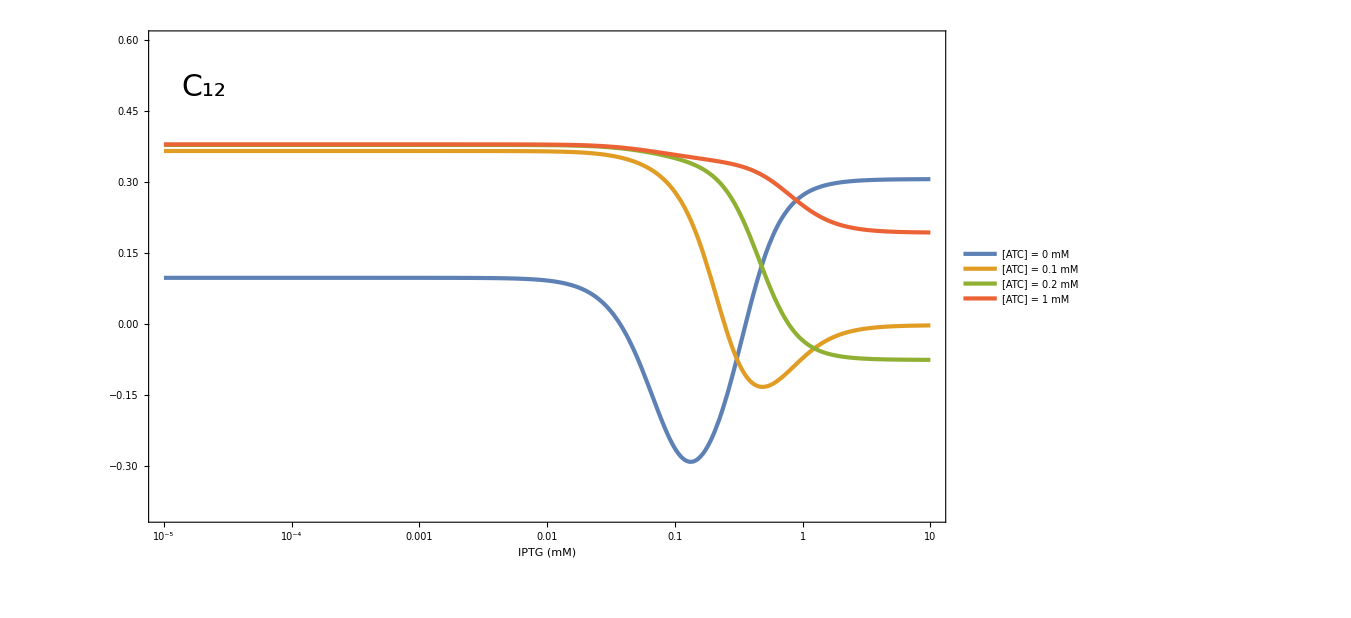

```mathematica
titleCoordCorrATC = {-10.8,0.5};
Gc12ATC= Show[LogLinearPlot[{C12[IPTG,0],C12[IPTG,0.1],C12[IPTG,0.2],C12[IPTG,1]},{IPTG,10^-5,10},Evaluate[optGen],Evaluate[optCorr],Evaluate[legendNoiseATC]],Graphics[Text[Style[ToExpression["C_{12}",TeXForm,HoldForm],Evaluate[titleSetIn]],Evaluate[titleCoordCorrATC]]],
Evaluate[imSize2]]
Export["/home/gutiloluis/61Monograph/images/lan-gc12ATC.png",Gc12ATC];
```